# Homework 4

## Exercise 1

## a)

```mathematica
(* Func draws from Weibull(2,λ) by Inversion *)
drawWeibull[λ_]:=Sqrt[-Log[RandomReal[]]]/λ;
```

```mathematica
(* Func outputs the central difference estimator D_ε(λ) for some ε *)
centrallD[λ_,ε_]:=(2^drawWeibull[λ+ε/2]-2^drawWeibull[λ-ε/2])/ε;
```

```mathematica
(* Func obtains the 'real' value dz=d/dλ E[2^X] where X~Weibull(2,λ) evaluated at λ *)
getTruedz[val_] := Module[{λ,dz,expectedValue,derivative},
(* Define the expression for E[2^X]*)
expectedValue=Integrate[2^x 2 Exp[-x^2 λ^2]x λ^2,{x,0,Infinity}];
(*Differentiate with respect to λ*)
derivative=D[expectedValue,λ];
λ=val;
dz=N[derivative];
dz
]
```

```mathematica
(* truedz = getTruedz[1/2] *)
```

```mathematica
truedz=-14.955038070286037
```

-14.955

```mathematica
(* Func estimates dz=d/dλ E[2^X] at λ where X~Weibull(2,λ) using the finite differences CMC with R replicates *)
FD[R_,λ_]:= Module[{},
Dλ=Table[centrallD[λ,R^(-1/6)],R];
dz=Mean[Dλ];
MSE= Mean[(truedz-Dλ)^2];
{dz,MSE}
]
```

```mathematica
FD[10000,1/2]
```

{-18.5275,2684.19}

## b)

```mathematica
(* Outputs the central difference estimator with common random numbers D_ε(λ) for some ε*)
centralDwithCRN [λ_,ε_]:=Module[{U},
U=RandomReal[];
centralD=(2^(Sqrt[-Log[U]]/(λ+ε/2))-2^(Sqrt[-Log[U]]/(λ-ε/2)))/ε;
centralD
]
```

```mathematica
(* Func estimates dz=d/dλ E[2^X] at λ where X~Weibull(2,λ) using the finite differences CMC with R replicates *)
FDwithCRN[R_,λ_]:= Module[{Dλ,dz,MSE,Var},
Dλ=Table[centralDwithCRN[λ,R^(-1/6)],R];
dz=Mean[Dλ];
MSE= Mean[(truedz-Dλ)^2];
Var=Variance[Dλ];
{dz,MSE,Var}
]
```

```mathematica
FDwithCRN[10000,1/2]
```

{-17.8961,1118.97,1110.44}

## c)

```mathematica
(* outputs value of h_λ(u) as defined in Latex *)
h[u_,λ_]:=2^(Sqrt[-Log[u]]/λ);
```

```mathematica
(* outputs estimator D(λ) as defined in Latex *)
estD[u_,λ_]:= -h[u,λ]Log[h[u,λ]]/λ;
```

```mathematica
(* estimates dz=d/dλ E[2^X] at λ where X~Weibull(2,λ) using IPA and CMC with R replicates  *)
IPA[R_,λ_]:= Module[{Dλ,dz,MSE,Var},
Dλ=Table[estD[RandomReal[],λ],R];
dz=Mean[Dλ];
MSE= Mean[(truedz-Dλ)^2];
Var=Variance[Dλ];
{dz,MSE,Var}
]
```

```mathematica
IPA[10000,1/2]
```

{-14.9046,678.995,679.061}

## d)

```mathematica
(* calculates D(λ) for Likelihood ratio as defined in the report *)
DLR[λ_]:= Module[{X},
X=drawWeibull[λ];
(4-X^2)2^X
]
```

```mathematica
(* estimates dz=d/dλ E[2^X] at λ where X~Weibull(2,λ) using IPA and CMC with R replicates  *)
LR[R_,λ_]:= Module[{Dλ,dz,MSE,Var},
Dλ=Table[DLR[λ],R];
dz=Mean[Dλ];
MSE= Mean[(truedz-Dλ)^2];
Var=Variance[Dλ];
{dz,MSE,Var}
]
```

```mathematica
LR[10000,1/2]
```

{-14.2263,5522.4,5522.43}

## Exercise 2

## a)

```mathematica
(* draws Gamma(2,β) *)
drawGamma[β_]:=-Log[RandomReal[]]/β-Log[RandomReal[]]/β;
```

```mathematica
(* defines function h(z) *)
h[z1_,z2_,z3_]:=Boole[Max[z1+z2,z3]≥ 3];
```

```mathematica
(* defines score func S(z) for θ_n *)
S[z1_,z3_,θ_] := 2z1/θ^2 -2/θ+2/(1-θ)-2z3/(3(1-θ)^2);
```

```mathematica
(* combines h(z)S(z) *)
hS[z1_,z2_,z3_,θ_] :=h[z1,z2,z3]S[z1,z3,θ];
```

```mathematica
(* gives D(θ_n) *)
dz[θ_,R_]:= Mean[Table[hS[drawGamma[2/θ],drawGamma[1],drawGamma[2/(3(1-θ))],θ],R]];
```

```mathematica
(* finds first n elements of the sequence θ_n *)
findθ[n_,θ0_,R_,C_]:= Module[{i,θ,previousθ,nextθ},
θ={θ0};
previousθ=θ0;
For[i=1,i≤n,i++,
While[True,
nextθ =previousθ-C/i dz[previousθ,R];
If[0<nextθ<1,Break[]];
];
θ=Append[θ,nextθ];
previousθ=nextθ;
];
θ
]
```

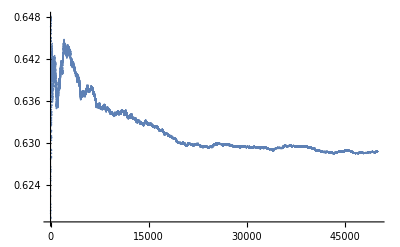

```mathematica
θ1=findθ[50000,0.5,10,0.2];
ListPlot[θ1]
```

```mathematica
θ1[[50000]]
```

0.628803

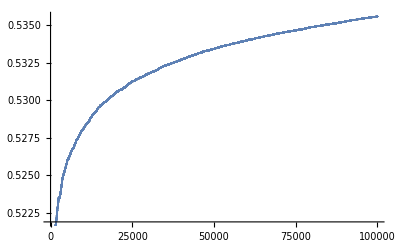

```mathematica
θ2=findθ[100000,0.5,10,0.02];
ListPlot[θ2]
```

```mathematica
θ2[[50000]]
```

0.533419

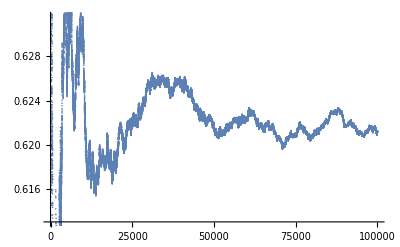

```mathematica
θ3=findθ[100000,0.5,10,1];
ListPlot[θ3]
```

```mathematica
θ3[[50000]]
```

0.621469